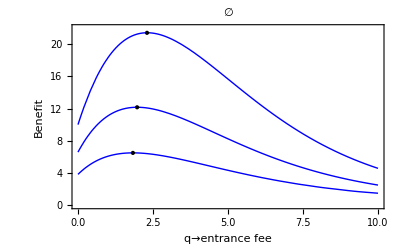

```mathematica
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α,q},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Show[{Plot[Evaluate@Table[a F Evaluate[{x[α,q][tmax]}/.sol]+q s (Evaluate[{y[α,q][tmax]}/.sol])^α Exp[-β q],{α,0,1,0.5}],{q,0,10},PlotRange->{0,22},PlotStyle->{Directive[Blue,Thick]},Frame->True,FrameLabel->{q->entrance fee,Benefit},LabelStyle->Bold, PlotLabel->∅],
Graphics[{Point[{1.83,6.50}],Point[{1.97,12.17}],Point[{2.30,21.43}]}]
}]]
```

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,q=1.83,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Table[s (Evaluate[{y[α][tmax]}/.sol])^α Exp[-β q],{α,0,0}]]
```

{{2.40473}}

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,q=1.97,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Table[s (Evaluate[{y[α][tmax]}/.sol])^α Exp[-β q],{α,0.5,1}]]
```

{{4.42805}}

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,q=2.30,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Table[s (Evaluate[{y[α][tmax]}/.sol])^α Exp[-β q],{α,1,1}]]
```

{{7.05797}}

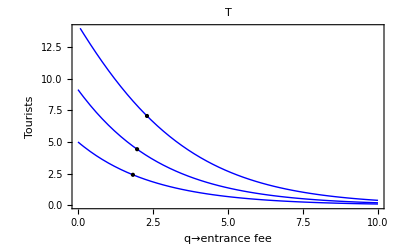

```mathematica
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α,q},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Show[{Plot[Evaluate@Table[s (Evaluate[{y[α,q][tmax]}/.sol])^α Exp[-β q],{α,0,1,0.5}],{q,0,10},PlotRange->{0,14},PlotStyle->{Directive[Blue,Thick]},Frame->True,FrameLabel->{q->entrance fee,Tourists},LabelStyle->Bold, PlotLabel->T],
Graphics[{Point[{1.83,2.4047306764288896}],Point[{1.97,4.428050466431007}],Point[{2.30,7.057968051480324}] }]
}]]
```

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,q=1.83,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Table[(Evaluate[{x[α][tmax]}/.sol]),{α,0,0}]]
```

{{2.10315}}

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,q=1.97,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Table[(Evaluate[{x[α][tmax]}/.sol]),{α,0.5,1}]]
```

{{3.45203}}

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,q=2.30,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Table[(Evaluate[{x[α][tmax]}/.sol]),{α,1,1}]]
```

{{5.20531}}

General::prng: Value of option PlotRange -> {0,Null} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

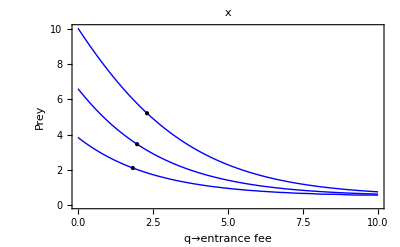

```mathematica
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α,q},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Show[{Plot[Evaluate@Table[Evaluate[{x[α,q][tmax]}/.sol],{α,0,1,0.5}],{q,0,10},PlotRange->{0,},PlotStyle->{Directive[Blue,Thick]},Frame->True,FrameLabel->{q->entrance fee,Prey},LabelStyle->Bold, PlotLabel->x],
Graphics[{Point[{1.83,2.103153784315629}],Point[{1.97,3.4520336442873383}],Point[{2.30,5.205312034320216}]}]
}]]
```

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,q=1.83,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Table[(Evaluate[{y[α][tmax]}/.sol]),{α,0.0,0.0}]]
```

{{3.98526}}

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,q=1.97,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Table[(Evaluate[{y[α][tmax]}/.sol]),{α,0.5,1}]]
```

{{3.79257}}

```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,q=2.30,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Table[(Evaluate[{y[α][tmax]}/.sol]),{α,1.0,1.0}]]
```

{{3.5421}}

General::prng: Value of option PlotRange -> {0,Null} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

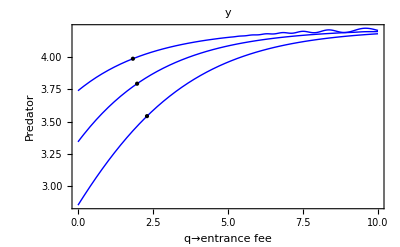

```mathematica
Module[{r=4,c=0.7,d=0.3,m=0.15,a=0.2,F=5,b=0.2,k=40,s=5,β=0.4,tmax=200},
sol=ParametricNDSolve[{x'[t]==r x[t](1-x[t]/k)-c x[t]y[t]-a F x[t],
y'[t]==d x[t]y[t]-m y[t]-b s (y[t])^(α+1)Exp[-β q],
x[0]==2,y[0]==1},{x,y},{t,0,tmax},{α,q},Method->{"EventLocator","Event"->{x[t],y[t]}},MaxSteps->10000(*AccuracyGoal->1*)];
Show[{Plot[Evaluate@Table[Evaluate[{y[α,q][tmax]}/.sol],{α,0,1,0.5}],{q,0,10},PlotRange->{0,},PlotStyle->{Directive[Blue,Thick]},Frame->True,FrameLabel->{q->entrance fee,Predator},LabelStyle->Bold, PlotLabel->y],
Graphics[{Point[{1.83,3.985263745068179}],Point[{1.97,3.792566622244666}],Point[{2.30,3.5420982808113983}]}]
}]]
```